## Race Prediction and Technique Analysis using FIS-Homologated Data

#### We would like a set of tools to better understand what makes a ski course hard, and how to do well on these hard courses.

We can download FIS homolgated race data from the FIS medias2.fis-ski.com website. This data is required for all ski events.

```mathematica
"https://medias2.fis-ski.com/pdf/homologations/CC/USA/USA_Black_Mountain__Rumford__Maine_18_18-04_5-0.pdf";
```

#### Processing Homologation Data

This data can be converted to a pixelmap using ImageValuePositions[] which we can render with HighlightImage

```mathematica
(*Fetch graph of homologation*)
pos=ImageValuePositions[-Graphics-, RGBColor[0.12435233160621761, 0.16580310880829016, 0.7098445595854922], .12];
HighlightImage[-Graphics-,{PointSize[Large],pos}]
```

-Graphics-

We want to analyse course elevation data and find slope/elevation along different points of the course. We define the length and height diff. of the actual course to convert pixel values to meaningful variables

```mathematica
(*comparison of pixel graph versus graph gives correct units*)

obsLenMax=5500;
obsLenMin=0;
obsHgtMax=310;
obsHgtMin=250;

obsHgtDiff=obsHgtMax-obsHgtMin;
obsLenDiff=obsLenMax-obsLenMin;

lenMax=Max[pos];
lenMin=Min[pos];
hgtMax=Max[Table[pos[[i]][[2]],{i,Length[pos]}]];
hgtMin=Min[Table[pos[[i]][[2]],{i,Length[pos]}]];
hgtDiff=hgtMax-hgtMin;
lenDiff=lenMax-lenMin;

v2Speed10Plus=4.43/4.81;
v1Speed10Plus=4.81/4.43;
v2Speed7Minus=11.53/10.90;
v1Speed7Minus=10.90/11.54;
```

We apply the corrections to the pixel graph, and plot the pixel graph with accurate dimensions

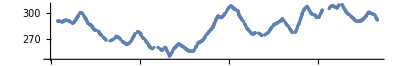

```mathematica
elevations=Table[{(obsLenDiff/lenDiff)(pos[[i]][[1]]-hgtMin),(obsHgtDiff/hgtDiff)(pos[[i]][[2]]-hgtMin)+obsHgtMin},{i,Length[pos]}];

ListPlot[Table[{(obsLenDiff/lenDiff)(pos[[i]][[1]]-hgtMin),(obsHgtDiff/hgtDiff)(pos[[i]][[2]]-hgtMin)+obsHgtMin},{i,Length[pos]}],AspectRatio->1/6,ImageSize->Full]
```

We can extract the MaxElevation with Select[elevations]

```mathematica
MaxElevation =Select[elevations,#[[2]]==Max[Map[Last,elevations]]&][[1]];
MaxElevation[[1]]/obsLenMax
```

0.891954

We can better understand the parsed data by interpolating it with Interpolation[DeleteDuplicatesBy[elevations,First]]

```mathematica
fitFunc=Interpolation[DeleteDuplicatesBy[elevations,First]]
(*create interpolation function to get smooth behav.*)
```

InterpolatingFunction[…]

For a first experiment, we can use some test data from a research study for v2/v1 speed on inclination to figure out how to best ski a FIS course. Later on, we will tackle more practical considerations, such as speed in L3/L4 on specific grades, and how technique choices can fatigue the skiers.

#### Extrapolate v1/v2 speed ratios at varying inclines using Linear-Regression (done with custom v1 vs. incline efficiency graphs part 2)

At 5% grade (1.05), v2 is 7% faster -> we can interpolate this data to a greater range with Predict["LinearRegression"], making a wider range of predictions

```mathematica
(*create efficiency graphs automatically based on data*)

w[x_,n_]:=Round[x,0.01]

p=Predict[{.07->1.05,.10->.92},Method->"LinearRegression"];

compData=MapThread[Rule,{(Range[15]*.01),If[p[#]>1,"v2","v1"]&/@(Range[15]*.01)}]

selector=Classify[compData];
```

We can plot the FIS race course, and create a colorList based on the kind of technique that is most efficient at each location.

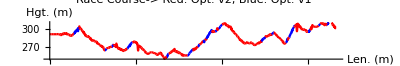

```mathematica
(*Default speed graphs given some pubmed data for xc skiing online*)
kind=Map[selector,Table[Values[elevationSlopeData[[j]]],{j,Length[elevationSlopeData]}]];

diffy=30;

elevationSlopeData=Table[{i,i+30}->w[(fitFunc[i+30]-fitFunc[i])/30,4],{i,1,5000-diffy,diffy}];

slopeData=Table[w[(fitFunc[i+30]-fitFunc[i])/30,4],{i,1,5000-diffy,diffy}];

colorList=Table[{{elevationSlopeData[[i]][[1]][[1]],elevationSlopeData[[i]][[1]][[2]]}->Switch[kind[[i]],"v2",RGBColor[1, 0, 0],"v1",RGBColor[0, 0, 1]]},{i,Length[kind]}];

heightData=Table[fitFunc[elevationSlopeData[[i]][[1]][[1]]],{i,Length[kind]}];

coloredRange=Table[{Keys[colorList[[j]][[1]]][[1]],Keys[colorList[[j]][[1]]][[2]],Values[colorList[[j]]][[1]]},{j,Length[colorList]}];

(*collates graphs*)

Show[Table[Plot[fitFunc[x],{x,Keys[colorList[[j]]][[1]][[1]],Keys[colorList[[j]]][[1]][[2]]},PlotStyle->Values[colorList[[j]]][[1]],PlotRange->{{0,5000},{250,310}}],{j,Length[coloredRange]}],ImageSize->Full,PlotLabel->"Race Course-> Red: Opt. v2, Blue: Opt. v1", AxesLabel->{"Len. (m)","Hgt. (m)"},AspectRatio->1/6]
```

#### Classify race-course sections into “v1” or “v2” (or v2-alt <-> downhill/turning tech.) based on v1-incline, v2-incline efficiency graphs.

Now we can take into account more practical considerations. We assume based on lactate/HR data we can determine v1/v2 speed %of max speed vs elevation. We want to use this graph data to predict for each individual athlete, which technique they should select on each part of the course. This simple model also allows us to determine what perturbations of the v1/v2 eff. vs elevation graphs have the most effect on athlete performance, since we can also determine now with this simple model a predicted race time. This model does assume, that the skier is taking the least path about the course, and that no turning technique boosts are accumulated, etc.

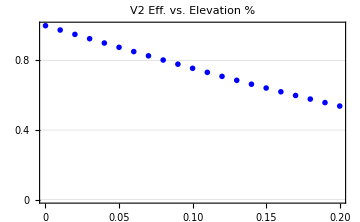
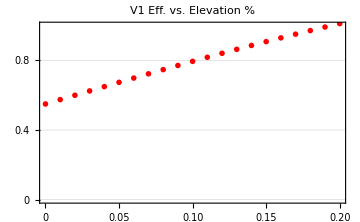

```mathematica
v2SpeedGraph=Table[i/100->{1-Tanh[i/40]+PDF[NormalDistribution[.25,.1],i/100]/20,"v2"},{i,0,20}];
v1SpeedGraph=Table[i/100->{.55+Tanh[i/40],"v1"},{i,0,20}];

ListPlot[Table[{i/100,1-Tanh[i/40]},{i,0,20}],PlotRange->{{0,.2},{0,1}},PlotLabel->Style["V2 Eff. vs. Elevation %",FontSize->12,FontFamily->"Helvetica"],PlotStyle->{Large,Blue}, PlotTheme->"Business",ImageSize->Medium]ListPlot[Table[{i/100,.55+Tanh[i/40]},{i,0,20}],PlotRange->{{0,.2},{0,1}},PlotLabel->Style["V1 Eff. vs. Elevation %",FontSize->12,FontFamily->"Helvetica"], PlotStyle->{Large,Red}, PlotTheme->"Business",ImageSize->Medium]
```

Assume a maxSpeed on flat of 4.47 m/sec, and a differential of 30. We calculate the slopetable for the race course, and determine at each quantized part of the course which technique provides what % of the max speed, and choose the largest one. Then we can use this data to predict the total race time.

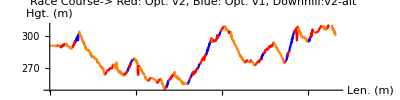

```mathematica
(*Custom speed graphs as a % of maximum speed vs. inclination for v1 and v2*)

maxSpeed=4.47(*meters/sec*);

diffy=30;

distanceTables=Table[Sqrt[((fitFunc[i+diffy]-fitFunc[i])^2+diffy^2)],{i,1,5000,diffy}];

slopeTable=Table[Values[elevationSlopeData[[i]]],{i,Length[elevationSlopeData]}];

Total[Table[distanceTables[[i]],{i,Length[distanceTables]}]];

bestApproachEff=Table[If[Values[v2SpeedGraph[[i]]][[1]]>Values[v1SpeedGraph[[i]]][[1]],Keys[v2SpeedGraph[[i]]]->{Values[v2SpeedGraph[[i]]][[1]],Values[v2SpeedGraph[[i]]][[2]]},Keys[v1SpeedGraph[[i]]]->{Values[v1SpeedGraph[[i]]][[1]],Values[v1SpeedGraph[[i]]][[2]]}],{i,Length[v1SpeedGraph]}];

bestPart=Table[Last[Switch[Select[bestApproachEff,slopeTable[[i]]>Keys[#1]&],{},0->{1.25,"v2-alt"},Except[_Empty],Last[Select[bestApproachEff,slopeTable[[i]]>Keys[#1]&]]]],{i,Length[slopeTable]}];

bestPart[[1]][[2]]
colorList=Table[{{elevationSlopeData[[i]][[1]][[1]],elevationSlopeData[[i]][[1]][[2]]}->Switch[bestPart[[i]][[2]],"v2",RGBColor[1, 0, 0],"v1",RGBColor[0, 0, 1],"v2-alt",Orange]},{i,Length[kind]}];

heightData=Table[fitFunc[elevationSlopeData[[i]][[1]][[1]]],{i,Length[kind]}];

coloredRange=Table[{Keys[colorList[[j]][[1]]][[1]],Keys[colorList[[j]][[1]]][[2]],Values[colorList[[j]]][[1]]},{j,Length[colorList]}];

Show[Table[Plot[fitFunc[x],{x,Keys[colorList[[j]]][[1]][[1]],Keys[colorList[[j]]][[1]][[2]]},PlotStyle->Values[colorList[[j]]][[1]],PlotRange->{{0,5000},{250,310}}],{j,Length[coloredRange]}],PlotLabel->Style["Race Course-> Red: Opt. v2, Blue: Opt. v1, Downhill:v2-alt",FontSize->18,FontFamily->"Helvetica"], AxesLabel->{"Len. (m)","Hgt. (m)"},ImageSize->Full,AspectRatio->1/4]
```

```mathematica
bestPart[[1]][[2]]
```

v2-alt

#### Calculate time on course given v1-v2/slope efficiency graphs

We can do what is essentially a line integral of sum_i speed_i *dist_i to get the total race time.

```mathematica
(*calulate time on course*)
v1SpeedGraph=Table[i/100->{.35+Tanh[i/40],"v1"},{i,0,20}];
v2SpeedGraph=Table[i/100->{1-Tanh[i/40]+PDF[NormalDistribution[.25,.1],i/100]/20,"v1"},{i,0,20}];
(*v2SpeedGraph=Table[g[i/100,3]->{g[1-Tanh[i/40],3],"v2"},{i,0,20}]*)

maxSpeed=4.47(*meters/sec*);

diffy=30;

distanceTables=Table[Sqrt[((fitFunc[i+diffy]-fitFunc[i])^2+diffy^2)],{i,1,5000,diffy}];

slopeTable=Table[Values[elevationSlopeData[[i]]],{i,Length[elevationSlopeData]}];

Total[Table[distanceTables[[i]],{i,Length[distanceTables]}]];

bestApproachEff=Table[If[Values[v2SpeedGraph[[i]]][[1]]>Values[v1SpeedGraph[[i]]][[1]],Keys[v2SpeedGraph[[i]]]->{Values[v2SpeedGraph[[i]]][[1]],Values[v2SpeedGraph[[i]]][[2]]},Keys[v1SpeedGraph[[i]]]->{Values[v1SpeedGraph[[i]]][[1]],Values[v1SpeedGraph[[i]]][[2]]}],{i,Length[v1SpeedGraph]}];

bestPart=Table[Last[Switch[Select[bestApproachEff,slopeTable[[i]]>Keys[#1]&],{},0->{1.25,"v2-alt"},Except[_Empty],Last[Select[bestApproachEff,slopeTable[[8]]>Keys[#1]&]]]],{i,Length[slopeTable]}];

Print["Minutes on Race Course ~ Sum* Delta_Distance * 1/Eff. * 1/Max Speed ~ Sum* Delta_Distance * speed. Div 60"]

Total[Table[Take[distanceTables,166][[i]]/bestPart[[i]][[1]]*(1/maxSpeed),{i,Length[bestPart]}]]/60
```

Minutes on Race Course ~ Sum* Delta_Distance * 1/Eff. * 1/Max Speed ~ Sum* Delta_Distance * speed. Div 60

17.2831

#### Perturb efficiency graphs with variable gaussian function to determine efficiency/incline weakness.

We add a modified gaussian function to different parts of the v2 speed graph to better understand what part of the v2 speed graph is the weakest link of the race performance, and could be a training focus. This formalizes the idea that we need to train at different inclinations to mimic the race courses we are looking to perform on. For example, if your v2 is weak at the higher inclinations, this could be a focus point for the athlete both technically and physically.

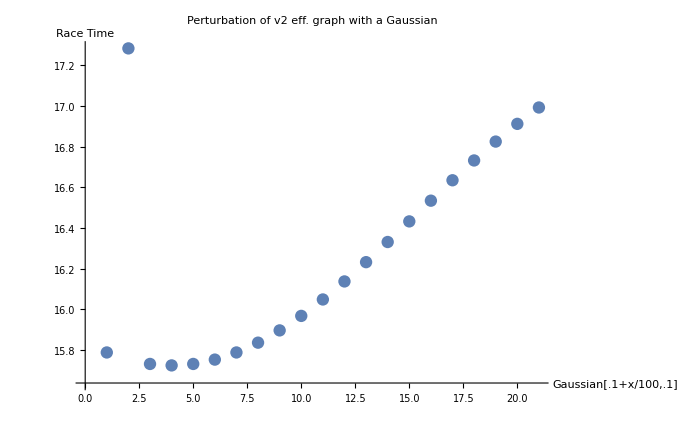

therefore, this v2 eff. graph could greatly improve performance if it were increased ~5/20 ~25% capacity~5% slope. therefore, v2 training at medium elevation is optimal

```mathematica
speedGraphsForV2=Table[Table[i/100->{1-Tanh[i/40]+PDF[NormalDistribution[j/100,.1],i/100]/20,"v2"},{i,0,20}],{j,0,20}];
(*v2SpeedGraph=Table[g[i/100,3]->{g[1-Tanh[i/40],3],"v2"},{i,0,20}]*)

perturbationGaussianV2Eff={#,getSpeedAdjustment[speedGraphsForV2[[#]],fitFunc,v1SpeedGraph,elevationSlopeData]}&/@Range[Length[speedGraphsForV2]];

ListPlot[perturbationGaussianV2Eff,PlotLabel->"Perturbation of v2 eff. graph with a Gaussian",AxesLabel->{"Gaussian[.1+x/100,.1]" ,"Race Time"}]

Print["therefore, this v2 eff. graph could greatly improve performance if it were increased ~5/20 ~25% capacity~5% slope. therefore, v2 training at medium elevation is optimal"]

getSpeedAdjustment[v2SpeedGraph,fitFunc,v1SpeedGraph,elevationSlopeData]:=Module[{},

maxSpeed=4.47(*meters/sec*);

diffy=30;

distanceTables=Table[Sqrt[((fitFunc[i+diffy]-fitFunc[i])^2+diffy^2)],{i,1,5000,diffy}];

slopeTable=Table[Values[elevationSlopeData[[i]]],{i,Length[elevationSlopeData]}];

Total[Table[distanceTables[[i]],{i,Length[distanceTables]}]];

bestApproachEff=Table[If[Values[v2SpeedGraph[[i]]][[1]]>Values[v1SpeedGraph[[i]]][[1]],Keys[v2SpeedGraph[[i]]]->{Values[v2SpeedGraph[[i]]][[1]],Values[v2SpeedGraph[[i]]][[2]]},Keys[v1SpeedGraph[[i]]]->{Values[v1SpeedGraph[[i]]][[1]],Values[v1SpeedGraph[[i]]][[2]]}],{i,Length[v1SpeedGraph]}];

bestPart=Table[Last[Switch[Select[bestApproachEff,slopeTable[[i]]>Keys[#1]&],{},0->{1.25,"v2-alt"},Except[_Empty],Last[Select[bestApproachEff,slopeTable[[8]]>Keys[#1]&]]]],{i,Length[slopeTable]}];

Total[Table[Take[distanceTables,166][[i]]/bestPart[[i]][[1]]*(1/maxSpeed),{i,Length[bestPart]}]]/60

]
```

```mathematica
AeTHR=.7;
LTHR=.8;
AeTMaxCap=Erf[.7]
LTMaxCap=Erf[.8]

{Plot[LTMaxCap-(LTMaxCap*x/20)^2,{x,0,20},PlotLabel->"LT Velocity vs Capacity", ImageSize->Medium],Plot[AeTMaxCap-(AeTMaxCap*x/50)^2,{x,0,50},PlotLabel->"AeT Velocity vs Minutes", ImageSize->Medium]};

Show[Plot[Erf[x],{x,0,1},GridLines->{{{.8,Directive[Thickness->.004,Red]},{.7,Directive[Thickness->.005,Purple]},{1.0,Directive[Thickness->.004,Blue]}},{0}},ImageSize->Large,PlotLabel->"HR & Max Capacity",AxesLabel->{"Effort (%HR)","Max Velocity"}],ListPlot[{{Callout[{.8,Erf[.8]},"LT",Right],Callout[{.7,Erf[.7]},"AeT",Right],Callout[{1,Erf[1.0]},"Max-HR",Left]}}]];
```

0.677801

0.742101

```mathematica
AeTDeclineCurve[5.36, AeTDeclineCurve]
```

```mathematica
diffy=30;

distanceTables=Table[Sqrt[((fitFunc[i+diffy]-fitFunc[i])^2+diffy^2)],{i,1,5000,diffy}];

slopeTable=Table[Values[elevationSlopeData[[i]]],{i,Length[elevationSlopeData]}];

Total[Table[distanceTables[[i]],{i,Length[distanceTables]}]];

bestApproachEff=Table[If[Values[v2SpeedGraph[[i]]][[1]]>Values[v1SpeedGraph[[i]]][[1]],Keys[v2SpeedGraph[[i]]]->{Values[v2SpeedGraph[[i]]][[1]],Values[v2SpeedGraph[[i]]][[2]]},Keys[v1SpeedGraph[[i]]]->{Values[v1SpeedGraph[[i]]][[1]],Values[v1SpeedGraph[[i]]][[2]]}],{i,Length[v1SpeedGraph]}];

bestPart=Table[Last[Switch[Select[bestApproachEff,slopeTable[[i]]>Keys[#1]&],{},0->{1.25,"v2-alt"},Except[_Empty],Last[Select[bestApproachEff,slopeTable[[8]]>Keys[#1]&]]]],{i,Length[slopeTable]}];


getCapacity[currentCapacity_, distance_, speed_]:=Module[{},


secs=distance/(speed*currentCapacity);

ActualMins=Values[Solve[LTMaxCap-(LTMaxCap*x/20)^2==.7,x,NonNegativeReals][[1]]][[1]]//Echo;

newCapacity=LTMaxCap-LTMaxCap*(ActualMins/20-(secs/60)/20)^2

]


distance =30
speed = 4

currentCapacity=.7

getCapacity[30,4,currentCapacity]

secs=distance/(speed*currentCapacity)

ActualMins=Values[Solve[LTMaxCap-(LTMaxCap*x/20)^2==.7,x,NonNegativeReals][[1]]][[1]]

newCapacity=LTMaxCap-LTMaxCap*(ActualMins/20-(secs/60)/20)^2

LTMaxCap-(LTMaxCap*33/20)^2
```

30

4

0.7

5.52985

0.685434

10.7143

5.52985

0.688974

-0.757217

```mathematica
Values[Solve[LTMaxCap-(LTMaxCap*x/20)^2==.3,x,NonNegativeReals][[1]]][[1]]
```

17.9196

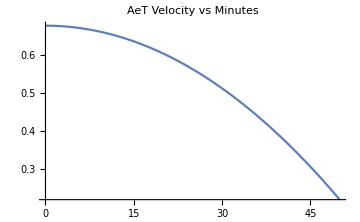

5.36913

1.25

```mathematica
Plot[AeTMaxCap-(AeTMaxCap*x/50)^2,{x,0,50},PlotLabel->"AeT Velocity vs Minutes", ImageSize->Medium]
```

```mathematica
-D[(AeTMaxCap-(AeTMaxCap*-x/50)^2), x]
```

0.000367532 x

```mathematica
ListPlot[Table[{i/100,1-Tanh[i/40]},{i,0,20}],PlotRange->{{0,.2},{0,1}},PlotLabel->Style["V2 Eff. vs. Elevation %",FontSize->12,FontFamily->"Helvetica"],PlotStyle->{Large,Blue}, PlotTheme->"Business",ImageSize->Medium]ListPlot[Table[{i/100,.55+Tanh[i/40]},{i,0,20}],PlotRange->{{0,.2},{0,1}},PlotLabel->Style["V1 Eff. vs. Elevation %",FontSize->12,FontFamily->"Helvetica"], PlotStyle->{Large,Red}, PlotTheme->"Business",ImageSize->Medium]
```

-Graphics- -Graphics-

```mathematica
(*calulate time on course*)
v1SpeedGraph=Table[i/100->{.35+Tanh[i/40],"v1"},{i,0,20}]
v2SpeedGraph=Table[i/100->{1-Tanh[i/40]+PDF[NormalDistribution[.25,.1],i/100]/20,"v1"},{i,0,20}]
(*v2SpeedGraph=Table[g[i/100,3]->{g[1-Tanh[i/40],3],"v2"},{i,0,20}]*)

maxSpeed=4.47(*meters/sec*);
```

```mathematica
diffy=30;

distanceTables=Table[Sqrt[((fitFunc[i+diffy]-fitFunc[i])^2+diffy^2)],{i,1,5000,diffy}];

slopeTable=Table[Values[elevationSlopeData[[i]]],{i,Length[elevationSlopeData]}];

Total[Table[distanceTables[[i]],{i,Length[distanceTables]}]];

bestApproachEff=Table[If[Values[v2SpeedGraph[[i]]][[1]]>Values[v1SpeedGraph[[i]]][[1]],Keys[v2SpeedGraph[[i]]]->{Values[v2SpeedGraph[[i]]][[1]],Values[v2SpeedGraph[[i]]][[2]]},Keys[v1SpeedGraph[[i]]]->{Values[v1SpeedGraph[[i]]][[1]],Values[v1SpeedGraph[[i]]][[2]]}],{i,Length[v1SpeedGraph]}];

bestPart=Table[Last[Switch[Select[bestApproachEff,slopeTable[[i]]>Keys[#1]&],{},0->{1.25,"v2-alt"},Except[_Empty],Last[Select[bestApproachEff,slopeTable[[8]]>Keys[#1]&]]]],{i,Length[slopeTable]}];

Print["Minutes on Race Course ~ Sum* Delta_Distance * 1/Eff. * 1/Max Speed ~ Sum* Delta_Distance * speed. Div 60"]

Total[Table[Take[distanceTables,166][[i]]/bestPart[[i]][[1]]*(1/maxSpeed),{i,Length[bestPart]}]]/60
```

Minutes on Race Course ~ Sum* Delta_Distance * 1/Eff. * 1/Max Speed ~ Sum* Delta_Distance * speed. Div 60

17.2831

```mathematica
Table[s[[1]][[i]],{i,10}]//TableForm
```

```mathematica
Off[InterpolatingFunction::dmval]
Off[General::stop]
Off[Classify::mincnb]
```

```mathematica
CloudPublish[]
```

CloudObject[https://www.wolframcloud.com/obj/e319e595-330a-439c-a3f2-71c6f3470b9d]

```mathematica
CopyToClipboard[CloudObject["https://www.wolframcloud.com/obj/e319e595-330a-439c-a3f2-71c6f3470b9d"]⟦1⟧]
```